```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/335/Книга1.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/335/Книга1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

```mathematica
dataset1=makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
line =LinearModelFit[Normal@dataset1[All,{"I","B"}/*Values],{1,x},x]
exp= NonlinearModelFit[Normal@dataset1[All,{"I","B"}/*Values],a(1-E^(-x/b)),{a,b},x]
```

FittedModel[90.0505+887.719 x]

FittedModel[1521.56 (1-ⅇ^(-1.0403 x))]

```mathematica
line["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 90.0505 | 55.606 | 1.61944 | 0.15648
x | 887.719 | 73.5456 | 12.0703 | 0.0000196317

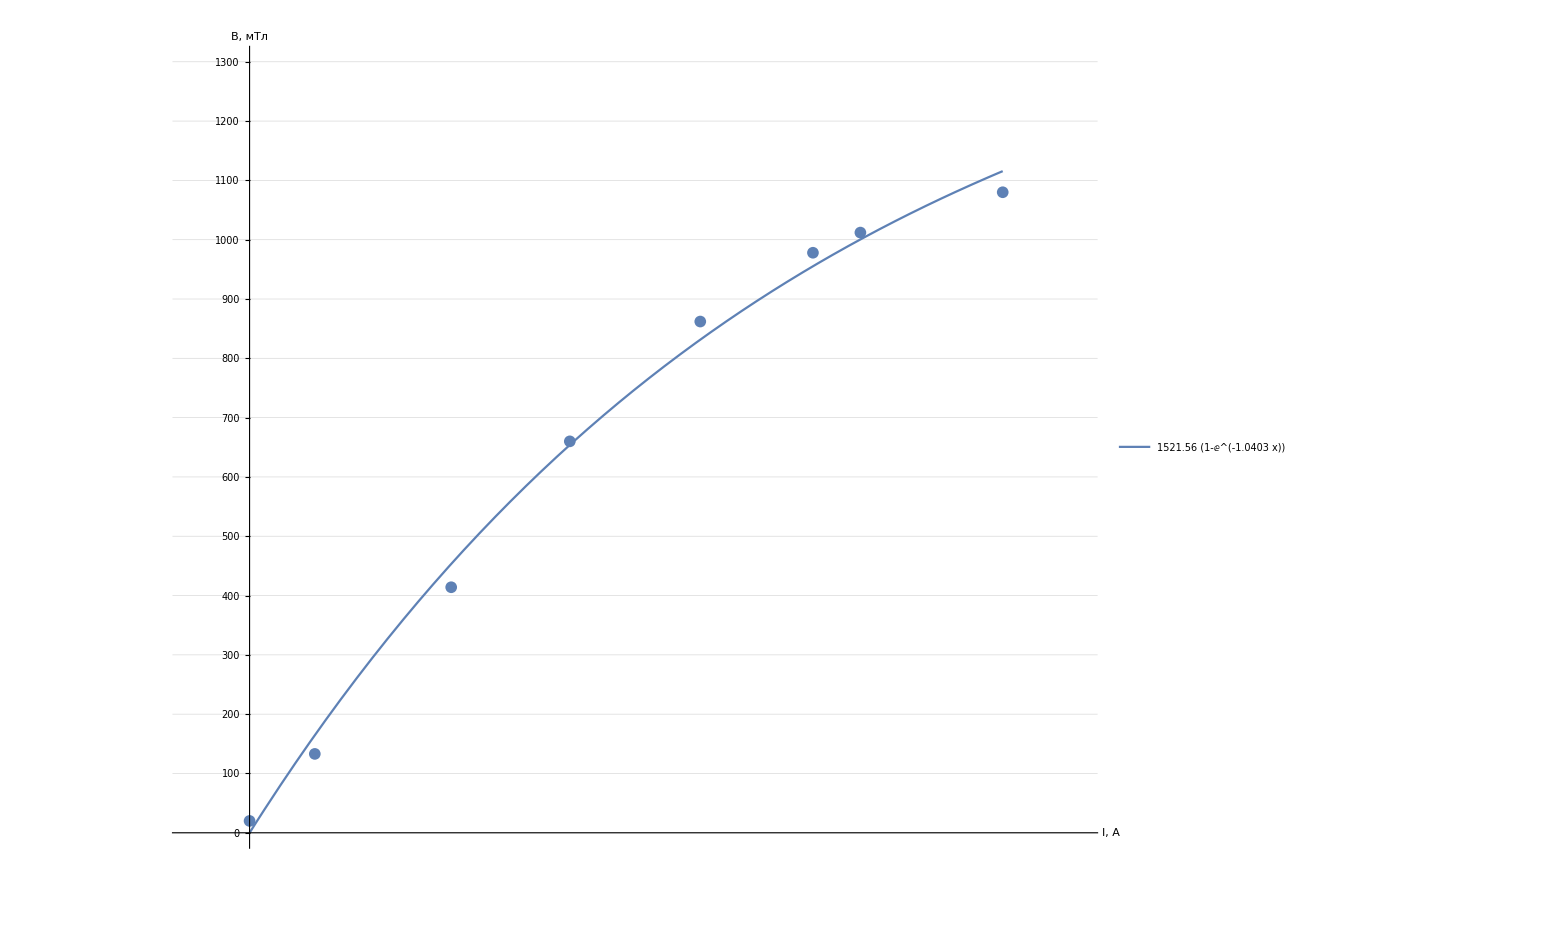

```mathematica
Show[
ListPlot[
{dataset1},
Ticks-> {Range[-10,10,0.1],Range[0,1300,100]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["I, А",Large],Style["В, мТл",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
PlotRange->{{-0.1,1.4},{0,1300}},
GridLines->{Range[-0.1,2,0.025], Range[-1500,1500,25]},
LabelStyle->Black
],
Plot[
{exp@x},
{x,0, 1.27},
PlotLegends->Placed[
LineLegend[
{Normal@exp},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
]
]
]
```

## Dataset2

```mathematica
dataset2=makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"B"->(Around[#B, #dB]&),"E"-> (Around[#E, #dE] &)|>]
```

Dataset[<>]

```mathematica
line2 =LinearModelFit[Normal@dataset2[All,{"B","E"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+0.000108875 x]

```mathematica
line2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 0.000108875 | 9.6281×10^-6 | 11.3081 | 0.00148325

## Dataset3

```mathematica
dataset3=makeDataset[raw⟦5⟧]
```

Dataset[<>]

```mathematica
dataset3WithErrs=dataset3[All,<|"B"->(Around[#B, #dB]&),"E"-> (Around[#E, #dE] &)|>]
```

Dataset[<>]

```mathematica
line3 =LinearModelFit[Normal@dataset3[All,{"B","E"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+0.000324975 x]

```mathematica
line3["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 0.000324975 | 0.0000186333 | 17.4405 | 2.27861×10^-6

## Dataset4

```mathematica
dataset4=makeDataset[raw⟦6⟧]
```

Dataset[<>]

```mathematica
dataset4WithErrs=dataset4[All,<|"B"->(Around[#B, #dB]&),"E"-> (Around[#E, #dE] &)|>]
```

Dataset[<>]

```mathematica
line4 =LinearModelFit[Normal@dataset4[All,{"B","E"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+0.000478521 x]

```mathematica
line4["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 0.000478521 | 0.0000162882 | 29.3784 | 1.9524×10^-9

## Dataset5

```mathematica
dataset5=makeDataset[raw⟦7⟧]
```

Dataset[<>]

```mathematica
dataset5WithErrs=dataset5[All,<|"B"->(Around[#B, #dB]&),"E"-> (Around[#E, #dE] &)|>]
```

Dataset[<>]

```mathematica
line5 =LinearModelFit[Normal@dataset5[All,{"B","E"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+0.000604731 x]

```mathematica
line5["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 0.000604731 | 0.0000169118 | 35.7579 | 6.94815×10^-12

## Dataset6

```mathematica
dataset6=makeDataset[raw⟦8⟧]
```

Dataset[<>]

```mathematica
dataset6WithErrs=dataset6[All,<|"B"->(Around[#B, #dB]&),"E"-> (Around[#E, #dE] &)|>]
```

Dataset[<>]

```mathematica
line6 =LinearModelFit[Normal@dataset6[All,{"B","E"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+0.000692208 x]

```mathematica
line6["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 0.000692208 | 0.00001986 | 34.8544 | 8.9578×10^-12

## Dataset7

```mathematica
dataset7=makeDataset[raw⟦9⟧]
```

Dataset[<>]

```mathematica
dataset7WithErrs=dataset7[All,<|"B"->(Around[#B, #dB]&),"E"-> (Around[#E, #dE] &)|>]
```

Dataset[<>]

```mathematica
line7 =LinearModelFit[Normal@dataset7[All,{"B","E"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+0.000789589 x]

```mathematica
line7["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 0.000789589 | 0.0000205866 | 38.3545 | 3.46297×10^-12

## Dataset8

```mathematica
dataset8=makeDataset[raw⟦10⟧]
```

Dataset[<>]

```mathematica
dataset8WithErrs=dataset8[All,<|"B"->(Around[#B, #dB]&),"E"-> (Around[#E, #dE] &)|>]
```

Dataset[<>]

```mathematica
line8 =LinearModelFit[Normal@dataset8[All,{"B","E"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+0.00081229 x]

```mathematica
line8["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 0.00081229 | 0.0000232453 | 34.9443 | 8.7318×10^-12

## Plot

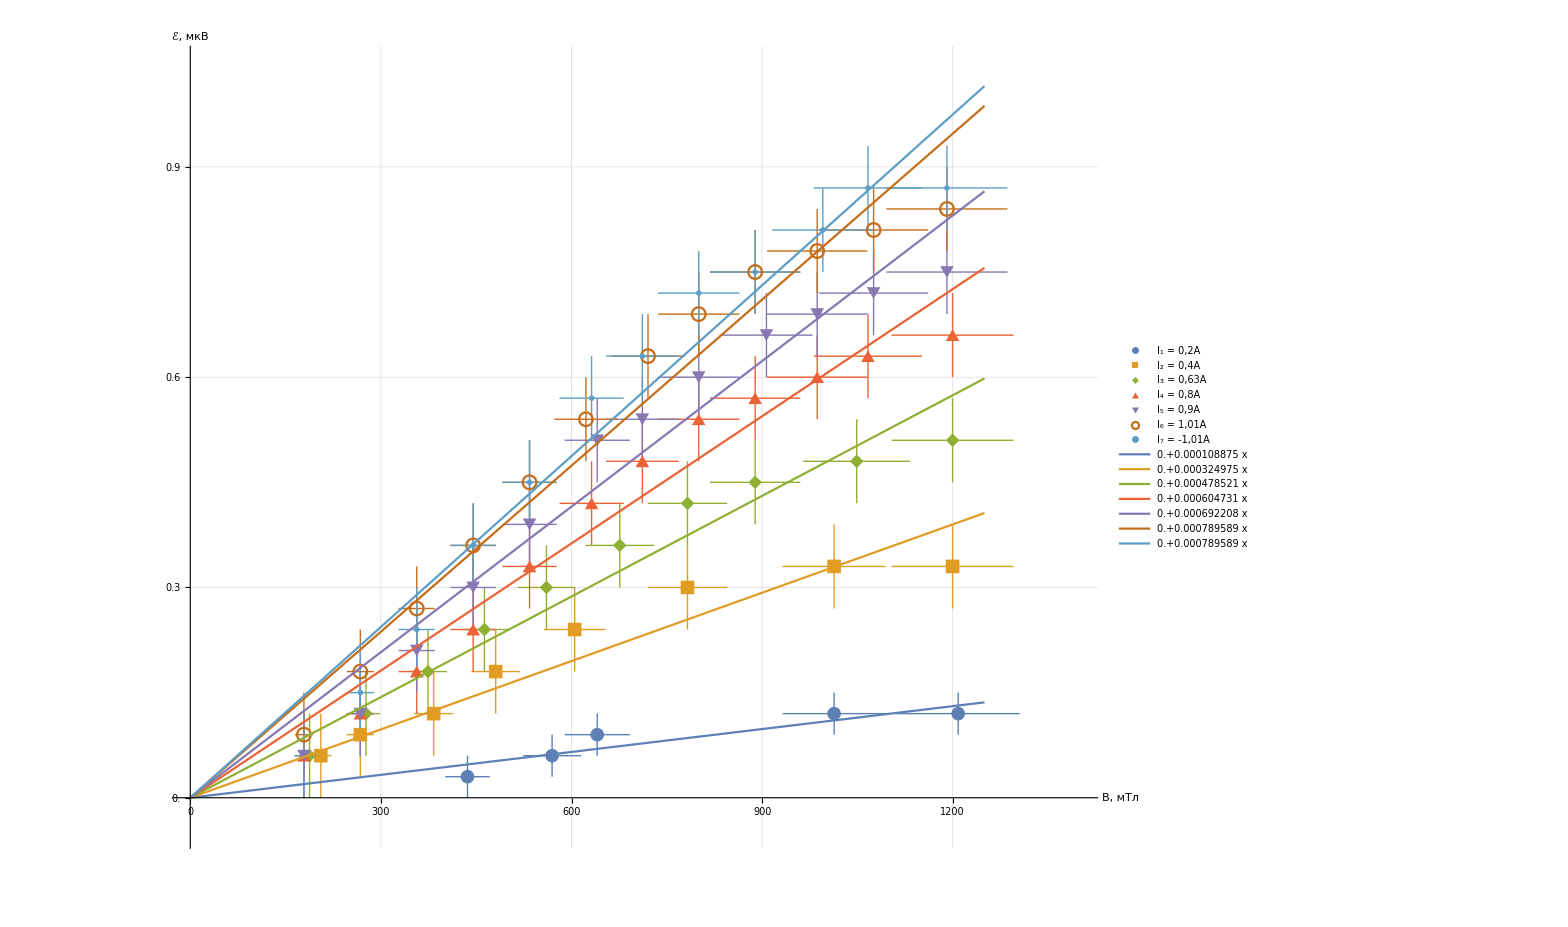

```mathematica
Show[
ListPlot[{dataset2WithErrs,dataset3WithErrs,dataset4WithErrs,dataset5WithErrs,dataset6WithErrs,dataset7WithErrs,dataset8WithErrs},
AxesLabel->{Style["B, мТл",Large],Style["ℰ, мкВ",Large]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->1500,
GridLines->{Range[0,5000,25], Range[-0.05,10,0.02]},
Ticks-> {Range[0,5000,100],Range[0,8,0.1]}, 
TicksStyle->20,
(*PlotStyle->Thickness[0.001]*)
PlotRange->{{0,1400},{-0.05,1.05}},
PlotMarkers->{Automatic,14},
PlotLegends->Placed[LineLegend[
Automatic,
{"I_1 = 0,2A","I_2 = 0,4A","I_3 = 0,63A","I_4 = 0,8A","I_5 = 0,9A","I_6 = 1,01A","I_7 = -1,01A"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18},
LegendLayout->"Row"
],
{Scaled[0.45],Scaled[0.85]}
]
],
Plot[
{line2@x,line3@x,line4@x,line5@x,line6@x,line7@x,line8@x},{x,0,1250},
(*PlotStyle->Thickness[0.002]*)
PlotLegends->Placed[
LineLegend
[
Automatic,
Normal/@{line2,line3,line4,line5,line6,line7,line7,line8},
LegendFunction->Framed,
LabelStyle->{FontSize->18}
],
{Scaled[0.15],Scaled[0.62]}
]
]
]
```

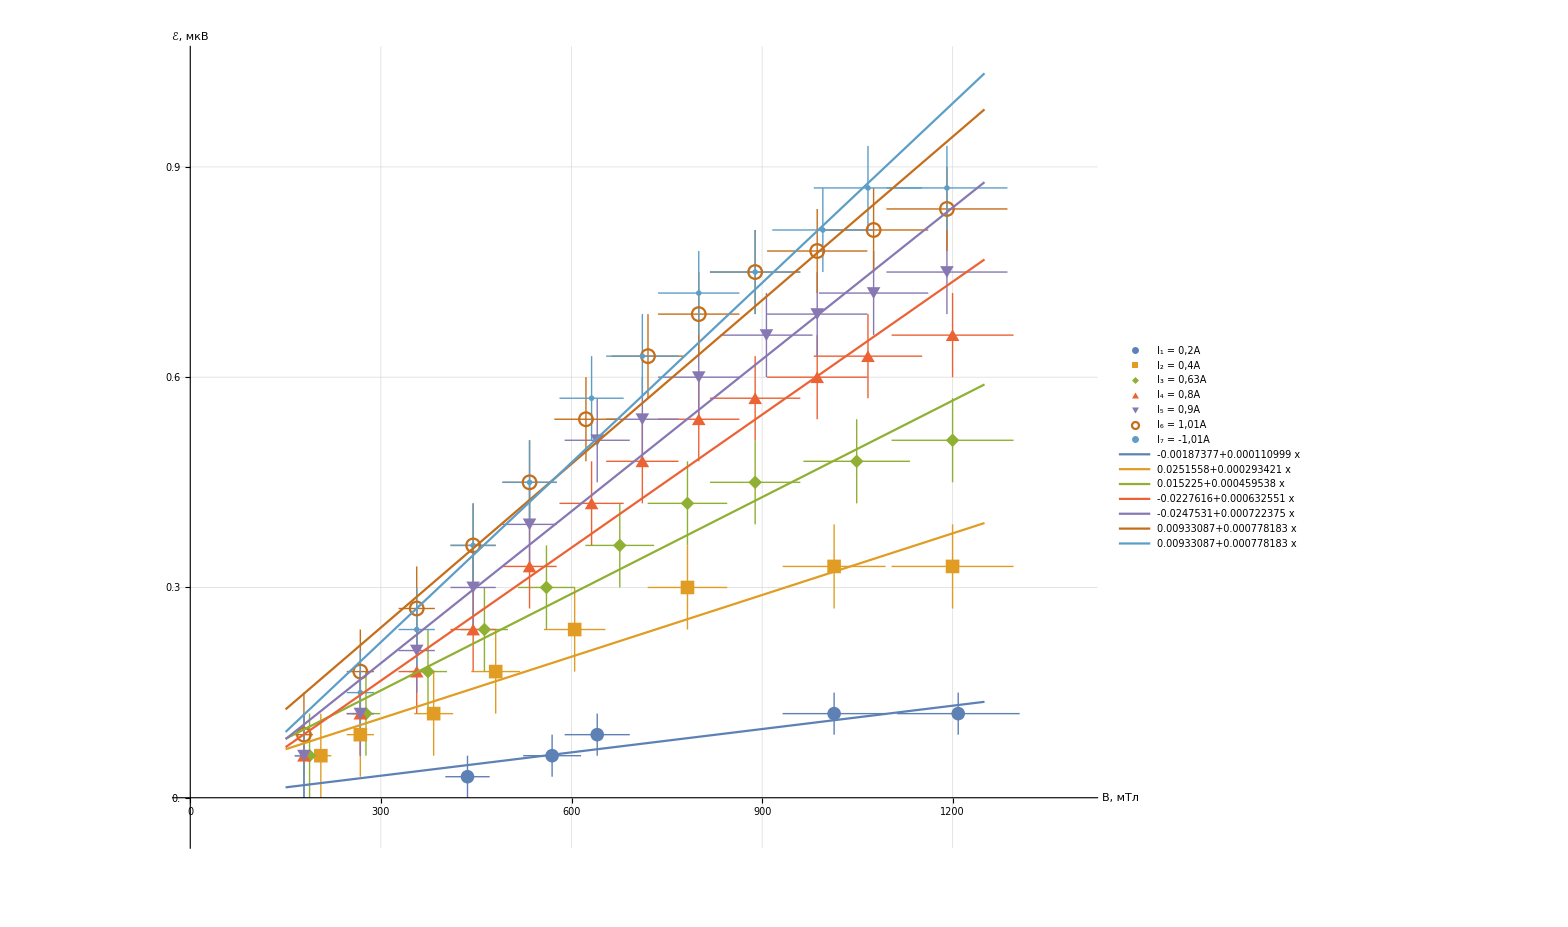

-Graphics-

## Dataset9

```mathematica
ClearAll[line9]
```

```mathematica
dataset9=makeDataset[raw⟦11⟧]
```

Dataset[<>]

```mathematica
dataset9WithErrs=dataset9[All,<|"I"->(#I&),"k"-> (Around[#k, #dk] &)|>]
```

Dataset[<>]

```mathematica
line9 =LinearModelFit[Normal@dataset9[All,{"I","k"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+772.498 x]

```mathematica
line9["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 772.498 | 13.7077 | 56.3551 | 3.32793×10^-8

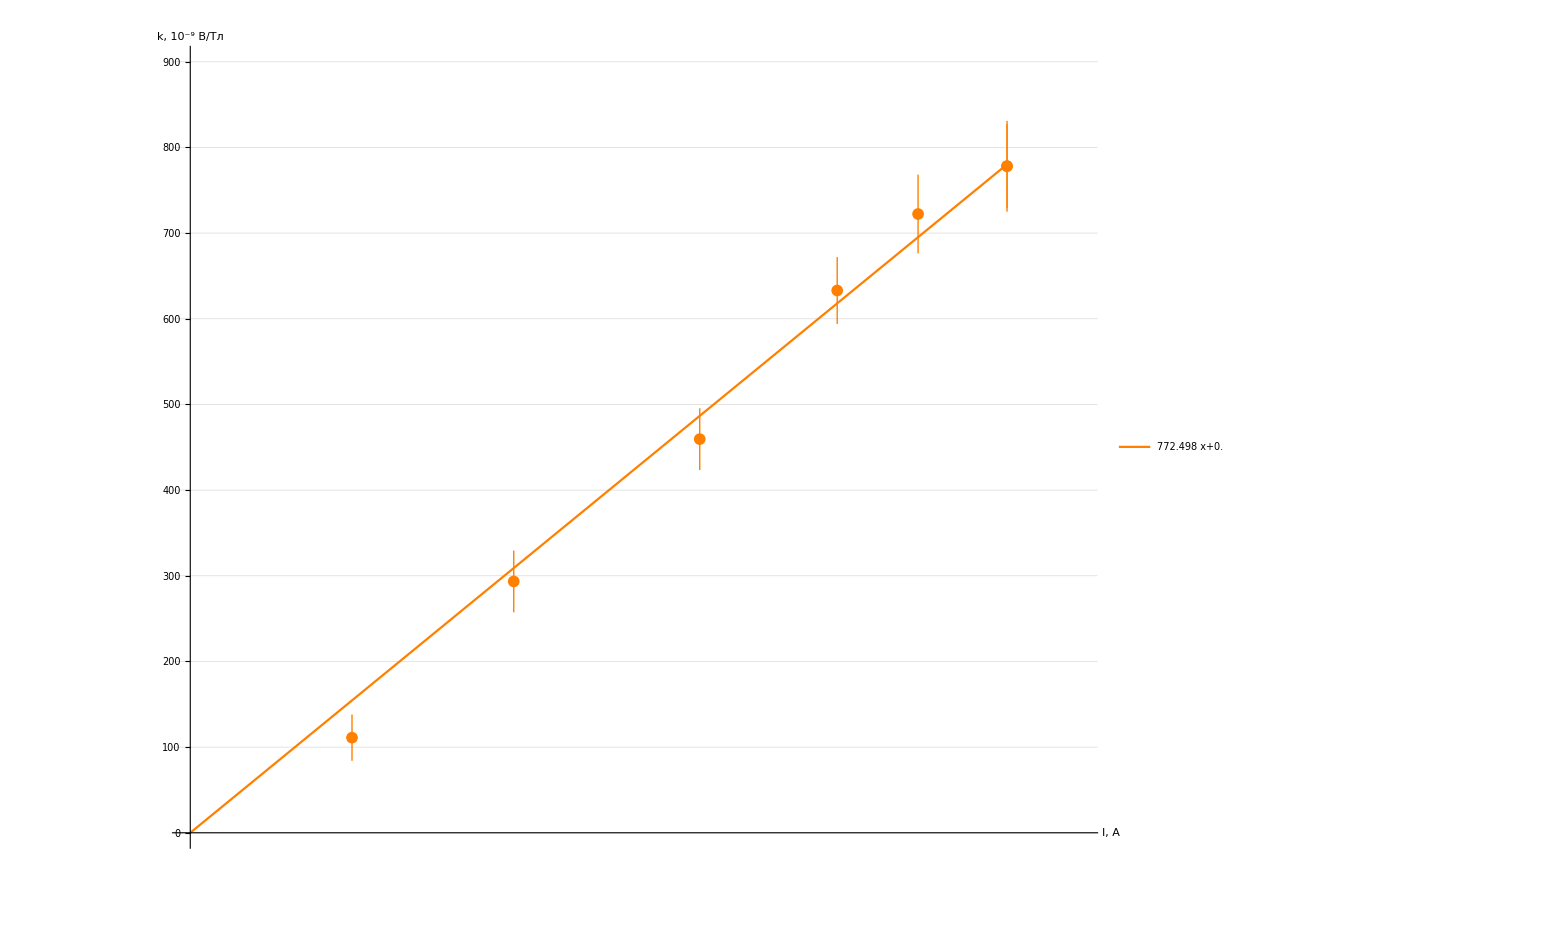

```mathematica
Show[
ListPlot[
{dataset9WithErrs},
Ticks-> {Range[-10,10,0.1],Range[0,1300,100]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["I, А",Large],Style["k, 10^-9 B/Тл",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
PlotRange->{{0,1.1},{0,900}},
GridLines->{Range[-0.1,2,0.025], Range[-1500,1500,25]},
LabelStyle->Black,
PlotStyle->Orange
],
Plot[
{line9@x},
{x,0, 1.01},
PlotLegends->Placed[
LineLegend[
{Normal@line9},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
],
PlotStyle->Orange
]
]
```

## Dataset10

```mathematica
dataset10 = makeDataset[raw⟦12⟧]
```

Dataset[<>]

```mathematica
dataset10WithErrs=dataset10[All,<|"B"->(Around[#B, #dB]&),"E"-> (Around[#E, #dE] &)|>]
```

Dataset[<>]

```mathematica
line10 =LinearModelFit[Normal@dataset10[All,{"B","E"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+0.000890974 x]

```mathematica
line10["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 0.000890974 | 0.0000212937 | 41.8421 | 1.45758×10^-12

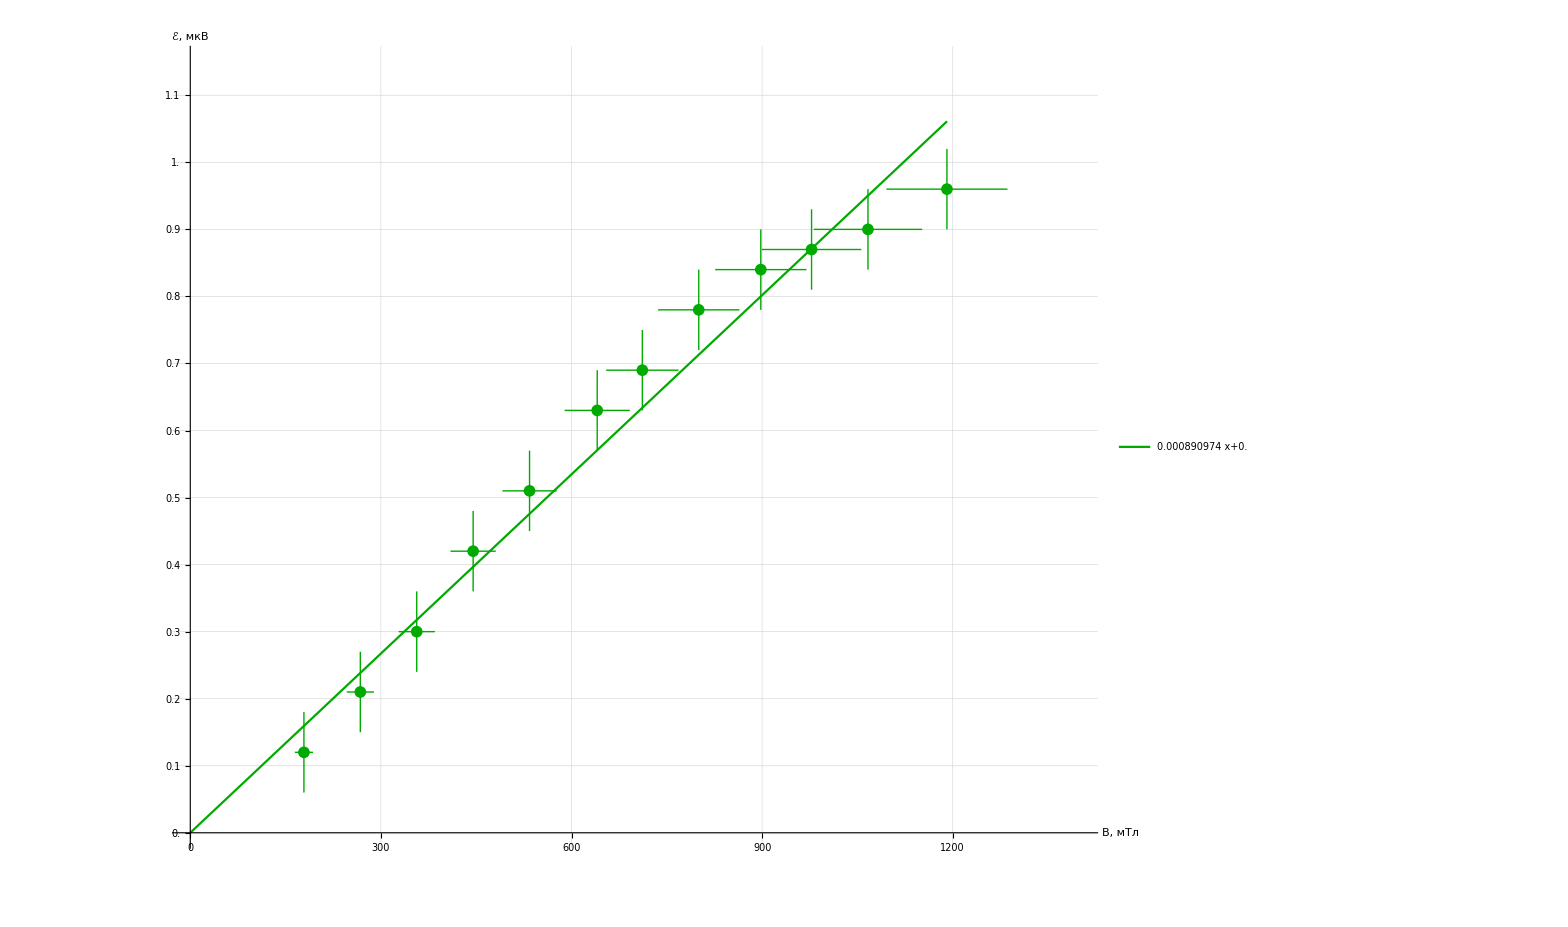

```mathematica
Show[
ListPlot[
{dataset10WithErrs},
Ticks-> {Range[0,10000,100],Range[0,2,0.1]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["B, мТл",Large],Style["ℰ, мкВ",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
PlotRange->{{0,1400},{0,1.15.00}},
GridLines->{Range[0,10000,25], Range[-10,10,0.05]},
LabelStyle->Black,
PlotStyle->Darker[Green]
],
Plot[
{line10@x},
{x,0, 1191},
PlotLegends->Placed[
LineLegend[
{Normal@line10},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
],
PlotStyle->Darker[Green]
]
]
```